```mathematica
copyNotebookDirectory
```

```mathematica
Get["/Users/johncosnett/Dropbox/05_PROGRAMS/001_LIFE/03_formula_to_cnf/cnf_programs/cnf2.m"];

output=StringReplace[updateIJ[({{0, 0, 0}, {0, 1, 0}, {0, 0, 0}})],rules];
export="p cnf 9 36 \n"<>output<>" 0";
ii=Export[NotebookDirectory[]<>"satproblem.txt",export]//Import;
SetDirectory[NotebookDirectory[]];
DeleteFile["satproblem.cnf"];
RenameFile["satproblem.txt","satproblem.cnf"];
ii
```

p cnf 9 36 
-1   -2   -3  0 
 -1   -2   -4  0 
 -1   -2   -6  0 
 -1   -2   -7  0 
 -1   -3   -4  0 
 -1   -3   -5  0 
 -1   -3   -6  0 
 -1   -3   -7   -9  0 
 -1   -7   -8  0 
 1   2   3  0 
 1   2   4   5   6   8   9  0 
 1   4   7  0 
 -2   -3   -4  0 
 -2   -3   -6  0 
 -2   -3   7  0 
 -2   -3   -9  0 
 -2   -5  0 
 -2   -6   7  0 
 -2   -8  0 
 2   3   4   5   6   7   8  0 
 -3   -8   -9  0 
 3   -4   -7  0 
 3   -4   -8  0 
 3   -5   -7  0 
 3   6   9  0 
 -4   -5  0 
 -4   -6  0 
 -4   -7   -8  0 
 -4   -7   -9  0 
 -5   -6  0 
 -5   -7   -9  0 
 -5   -8  0 
 -6   -7   -8  0 
 -6   -7   -9  0 
 -6   -8   -9  0 
 7   8   9 0

```mathematica
Import["/Users/johncosnett/Dropbox/05_PROGRAMS/001_LIFE/03_formula_to_cnf/cnf_programs/satproblem1output.txt"]
```

s SATISFIABLE
v -1 2 3 -4 -5 -6 7 -8 -9 0

```mathematica
life33
```

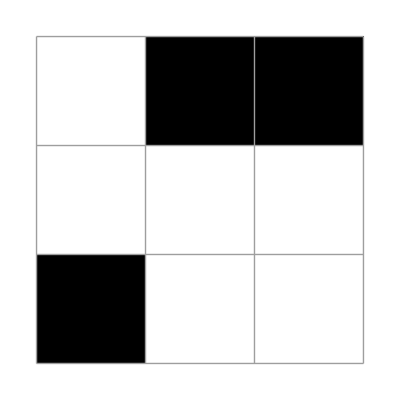
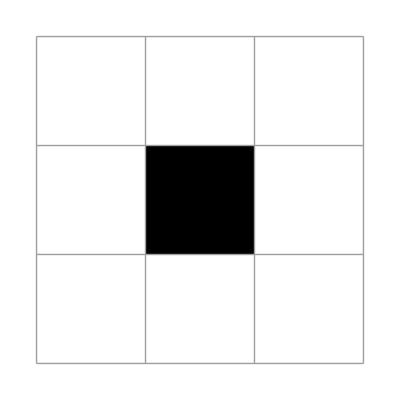

```mathematica
X1=({{0, 1, 1}, {0, 0, 0}, {1, 0, 0}});
plt/@NestList[updateLife[ #]&,
X1,1]
```

```mathematica
|
```

```mathematica
updateIJ[({{0, 0, 0}, {0, 1, 0}, {0, 0, 0}})]
```

{{0,1,1},{0,0,0},{1,0,0}}